# Практикум №5. Знакомство с графикой

Выполнил студент ММФ  БГУ
КМ, 1 к, 3 гр . Шпак А . В .
 07 ноября 2021

## 1. Секущая прямая к заданной кривой.

### Задание 1.

Постройте функцию CurveSecant[f,x_0,x_1,dx], которая отображает заданную кривую y=f(x) и секущую по отношению к ней прямую, проходящую через точки с абсциссами x_0<x_1 из области определения функции y=f(x). Аргумент dx задает приращения x_0-dx, x_1+dx абсцисс.

```mathematica
(*Я строю секущую графика функции y = f(x).*)
(*Две различные точки, принадлежащие кривой, и через которые проходит искомая секущая прямая, отображу как отдельные графические объекты.*)
(*Пусть эти точки имеют координаты {x0, f(x0)},{x1, f(x1)}.*)
(*Строю эти точки с помощью Point и чистой функции, которая, в моём случае, вернёт список из двух точек.*)
Point[{#,f[#]}]&/@{x0,x1}
```

{Point[{x0,f[x0]}],Point[{x1,f[x1]}]}

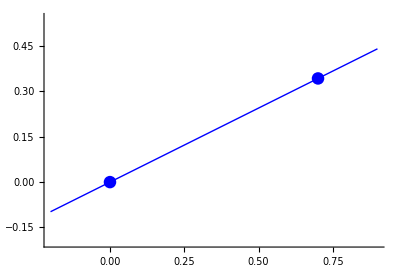

```mathematica
(*Чтобы построить секущую прямую, использую примитив Line. Для него указываю координаты точек, которые принадлежат секущей прямой, и абсциссы которых лежат левее меньшей координаты x0 и правее большей координаты x1.*)
(*Функция CurveSecant[f, x0, x1, dx] отображает секущую по отношению к кривой y=f(x) прямую, проходящую через точки кривой с абсциссами x0 и x1, x0 < x1. Аргумент dx задает приращения этих абсцисс оговоренные выше.*)
(*С поомщью AbsolutePointSize[d] указываю, что последующие точки показываются, если возможно, как окружности с диаметром d.*)
(*Hue задаёт цвет.*)
(*Примитиву Line задаю координаты начала и конца линии секущей: (x0 - dx, (k=(f[x1]-f[x0])/(x1-x0))(-dx)+f[x0]) и (x1 + dx + f[x0], k(x1+dx-x0)+f[x0])*)
Secant[f_,x0_,x1_,dx_]:=Graphics[{AbsolutePointSize[9],Hue[2/3],Point[{#,f[#]}]&/@{x0,x1},Line[{{x0-dx,(k=(f[x1]-f[x0])/(x1-x0))(-dx)+f[x0]},{x1+dx,k(x1+dx-x0)}+f[x0]}]},Axes->True,PlotRange->{{x0-dx,x1+dx},{f[x0]-dx,f[x1]+dx}}]
Secant[Power[#,3]&,0,.7,.2]
```

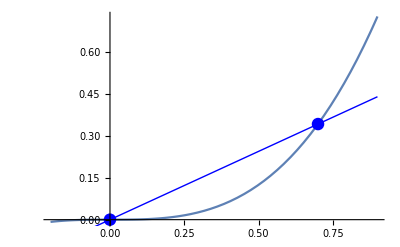

```mathematica
(*Функция CurveSecant[f, x0, x1, dx] строит график функции y=f(x) и секущую этого графика*)
CurveSecant[f_,x0_,x1_,dx_]:=Show[Plot[f[x],{x,x0-dx,x1+dx}],Secant[f,x0,x1,dx]]
CurveSecant[Power[#,3]&,0,.7,.2]
```

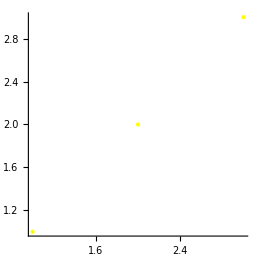

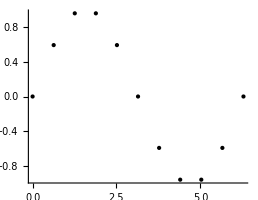

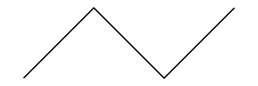

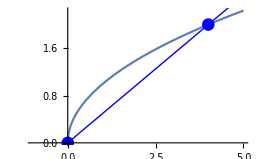

```mathematica
(*ПРИМЕРЫ.*)
(*Функция Graphics представляет возможность отобразить графические объекты в двухмерном виде.*)
Graphics[{PointSize[Large],Yellow,Point[{{1,1},{2,2},{3,3}}]},Axes->True]
Graphics[Point[Table[{t,Sin[t]},{t,0,2π,2π/10}]],Axes->True]
Graphics[Line[{{1,0},{2,1},{3,0},{4,1}}]]
CurveSecant[Sqrt[#]&,0,4,1]
```

## 2. Замкнутая ломаная.

### Задание 2.

Постройте функцию, вычисляющую графическое представление замкнутой ломаной.

```mathematica
(*ТЕОРИЯ И ЧТО Я БУДУ ДЕЛАТЬ. Ломаная линия – это объединение отрезков, в котором конец каждого
отрезка (кроме, возможно, последнего) является началом следующего отрезка, причем отрезки, имеющие общий конец, не лежат на одной прямой.*)
(*Ломаная
линия замкнута, если конец последнего отрезка совпадает с началом первого
отрезка.*)
(*Концы отрезков называют вершинами ломаной; отрезки, составляющие ломаную, – звеньями ломаной; отрезки, имеющие общий
конец – с межными звеньями ломаной.*)
(*Для построения замкнутой ломаной в Mathematica мне понадобится указать список точек, координат вершин ломаной, а также количество вершин*)
(*Замкнутую линию представлю в виде выражения BreakLine[Counter, Verticies], где Counter - количество вершин, а Verticies - список координат вершин.*)
(*В итоге я хочу построить функцию ShowBreakLine, которая отобразит мою замкнутуб ломаную BreakLine.*)
(*Глобальное определение функции будет иметь вид: ShowBreakLine[BL_BreakLine]:=FunctionBody. Она будет отражать вершины замкнутой ломаной, звенья и порядковые номера помледовательно поступажющих точек-вершин.]*) (*ЧТобы всё получилось, для начала научусь последовательно строить указанные выше элементы: отображу вершины, добавлю звенья и, наконец, для каждой точки вершины ломаной линии укажу порядковый номер её поступления.*)
(*НАЧИНАЮ ПОСТРОЕНИЕ. Сгенерирую произвольный экземпляр объекта типа BreakLine, задав координаты точек произвольным образом.*)
(*Генерирую Table'ом список значений рандомное количество рандомных координат.*)
Size=50;
P=Table[{RandomInteger[Size],RandomInteger[Size]},{RandomInteger[{3,15}]}];
BL=BreakLine[Length[P],P]
(*Генерирую объект BreakLine, состоящий из списка координат и их количества.*)
```

BreakLine[8,{{38,15},{38,6},{22,42},{7,36},{42,1},{12,3},{10,42},{40,43}}]

```mathematica
(*Строю вершины замкнутой ломаной с помощью Point.*)
(*С помощью Part показываю список координат.*)
BL[[2]]
```

{{38,15},{38,6},{22,42},{7,36},{42,1},{12,3},{10,42},{40,43}}

```mathematica
(*Получаю список точек.*)
Point[#]&/@BL[[2]]
```

{Point[{38,15}],Point[{38,6}],Point[{22,42}],Point[{7,36}],Point[{42,1}],Point[{12,3}],Point[{10,42}],Point[{40,43}]}

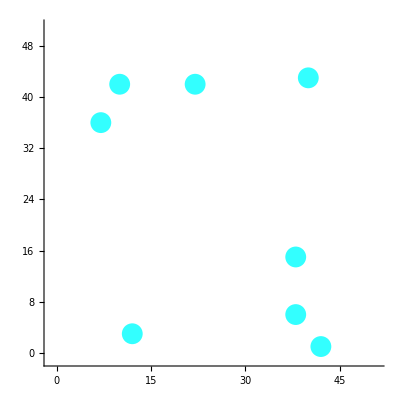

```mathematica
(*Строю выражение, которое создает и отображает вершины замкнутой ломаной как графический объект. Ассоциирую это вычисленное выражение с символом Fig1*)
(*AspectRatio определяет отношение высоты к ширине для графика.*)
Fig1=Graphics[{AbsolutePointSize[15],Hue[.5,.8,1],Point[#]&/@BL[[2]]},AspectRatio->Automatic,PlotRange->{{-1,Size+1},{-1,Size+1}},Axes->True]
```

```mathematica
(*Построю звенья ломаной линии BL, использую графический примитив Line. Чтобы замкнуть звенья,добавляю первую вершину в конец списка координат вершин.*)
{Hue[0.051],Append[BL[[2]],BL[[2,1]]]//Line}
(*Append даёт выражение с добавленным в конец элементом.*)
```

{Hue[0.051],Line[{{38,15},{38,6},{22,42},{7,36},{42,1},{12,3},{10,42},{40,43},{38,15}}]}

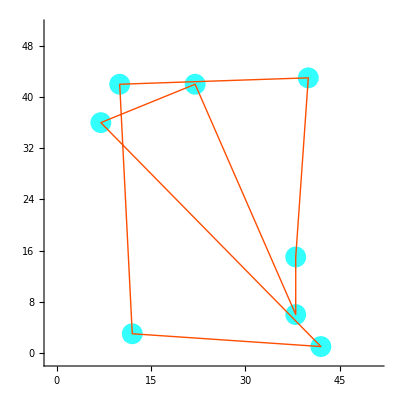

```mathematica
(*Строю выражение, которое строит и отображает звенья BreakLine как графический объект. Ассоциирую это вычисленное
выражение с символом Fig2.*)
Fig2=Graphics[{{AbsolutePointSize[15],Hue[.5,.8,1],Point[#]&/@BL[[2]]},{Hue[0.051],Append[BL[[2]],BL[[2,1]]]//Line}},AspectRatio->Automatic,PlotRange->{{-1,Size+1},{-1,Size+1}},Axes->True]
```

```mathematica
(*Попробую выполнить следующую задачу: подписать вершины ломаной линии BL в порядке их следования в списке.*)(*Для этого я использую функцию MapIndexed[func,expr,levelspec] и графический примитив Text*)(*Аргумент func является функцией двух переменных. Для различения первого и второго аргументов
функции func используют символы #1 и #2, соответственно.*)
(*При вычислении функции MapIndexed на место первого #1 аргумента функции func подставляется очередное подвыражение выражения expr, стоящее на уровне, указываемом levelspec.*)(*На место второго #2 аргумента func - позиция этого подвыражения в структуре выражения expr. По умолчанию, когда MapIndexed вызывается только с двумя аргументами, в выражении expr обрабатываются только подвыражения первого уровня.*)
(*Выражение BL[[2]] является списком, каждый элемент которого – список представляющий координаты одной вершины ломаной. Поэтому для отображения номера вершины используем ее позицию (#2) в списке BL[[2]].*)
MapIndexed[Text[First@#2,#1]&,BL[[2]]]
```

{Text[1,{38,15}],Text[2,{38,6}],Text[3,{22,42}],Text[4,{7,36}],Text[5,{42,1}],Text[6,{12,3}],Text[7,{10,42}],Text[8,{40,43}]}

```mathematica
(*А теперь отображение и точки, и её номера.*)
MapIndexed[{{Point[#1]},Text[First@#2,#1]}&,BL[[2]]]
```

{{{Point[{38,15}]},Text[1,{38,15}]},{{Point[{38,6}]},Text[2,{38,6}]},{{Point[{22,42}]},Text[3,{22,42}]},{{Point[{7,36}]},Text[4,{7,36}]},{{Point[{42,1}]},Text[5,{42,1}]},{{Point[{12,3}]},Text[6,{12,3}]},{{Point[{10,42}]},Text[7,{10,42}]},{{Point[{40,43}]},Text[8,{40,43}]}}

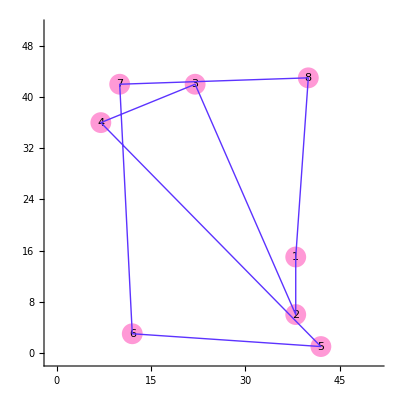

```mathematica
(*А теперь отображу полностью объект BreakLine вместе с точками, замкнутыми и их описанием.*)
Fig3=Graphics[{AbsolutePointSize[15],MapIndexed[{{Hue[.9,.4,1],Point[#1]},Text[First@#2,#1]}&,BL[[2]]],Hue[.7,.8,1],Append[BL[[2]],BL[[2,1]]]//Line},AspectRatio->Automatic,PlotRange->{{-1,Size+1},{-1,Size+1}},Axes->True]
```

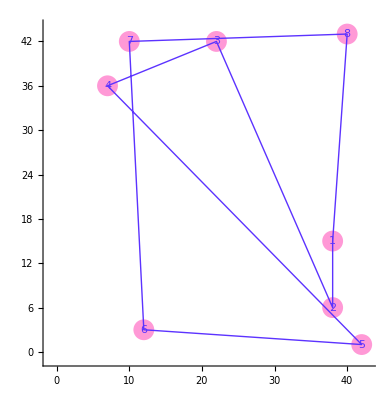

```mathematica
(*Обобщая все выполненные ранее построения, построю функцию showBreakLine. Определяю на выражениях,имеющих структуру вида BreakLine*)
ClearAll[showBreakLine]
showBreakLine[BL_BreakLine]:=Graphics[{AbsolutePointSize[15],Hue[.9,.4,1],Point[#]&/@BL[[2]],Hue[.7,.8,1],Line[Append[BL[[2]],BL[[2,1]]]],MapIndexed[{Text[First@#2,#1]}&,BL[[2]]]},AspectRatio->Automatic,Axes->True,PlotRange->{{-1,Max[Table[BL[[2,i,1]],{i,1,Length[BL[[2]]]}]]+1},{-1,Max[Table[BL[[2,i,2]],{i,1,Length[BL[[2]]]}]]+1}}]
showBreakLine[BL]
```

```mathematica
(*Периметр:*)
Append[BL[[2]],BL[[2,1]]]
```

{{38,15},{38,6},{22,42},{7,36},{42,1},{12,3},{10,42},{40,43},{38,15}}

```mathematica
getDistBetwPoints[coordA_List,coordB_List]:=Sqrt[(coordB-coordA).(coordB-coordA)]//N
```

```mathematica
Append[BL[[2]],BL[[2,1]]][[2]]-Append[BL[[2]],BL[[2,1]]][[1]]
```

{0,-9}

```mathematica
vectorCoords=Append[BL[[2]],BL[[2,1]]][[#+1]]-Append[BL[[2]],BL[[2,1]]][[#]]&/@Range[1,Length[BL[[2]]]]
```

{{0,-9},{-16,36},{-15,-6},{35,-35},{-30,2},{-2,39},{30,1},{-2,-28}}

```mathematica
getDistBetwPoints[{0,-9},{-16,36}]
getDistBetwPoints[{-16,36},{-15,-6}]
getDistBetwPoints[{-15,-6},{35,-35}]
getDistBetwPoints[{35,-35},{-30,2}]
getDistBetwPoints[{-30,2},{-2,39}]
getDistBetwPoints[{-2,39},{30,1}]
getDistBetwPoints[{30,1},{-2,-28}]
```

47.7598

42.0119

57.8014

74.793

46.4004

49.679

43.1856

```mathematica
Table[getDistBetwPoints[vectorCoords[[i+1]],vectorCoords[[i]]],{i,1,Length[vectorCoords]-1}]
```

{47.7598,42.0119,57.8014,74.793,46.4004,49.679,43.1856}

```mathematica
Plus@@Table[getDistBetwPoints[vectorCoords[[i+1]],vectorCoords[[i]]],{i,1,Length[vectorCoords]-1}]
```

361.631

## 3. График параметрической функции.

### Задание 3.

1) Постройте график функции, заданной параметрическими уравнениями. Используйте встроенную функцию ParametricPlot.
2) Напишите выражение, которое вычисляет список координат n точек, принадлежащих графику функции, заданной параметрическими уравнениями.
3) Отобразите в одной графической области график функции из п.1 и точки, вычисленные в п.2. Над каждой точкой укажите значение параметра, при котором вычислены ее координаты.
Вариант 9.

```mathematica
(*1) Строю график функции, заданной параметрически:*)
x[t_]:=Sqrt[t-1]
y[t_]:=1/Sqrt[t-1]
(*Анализируя x(t), y(t), получаю неравенство для нахождения области определения:*)
Reduce[Sqrt[t-1]>0]
```

t>1

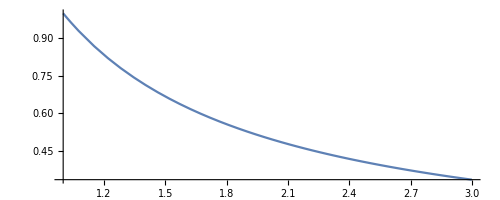

```mathematica
(*Строю график, опираясь на результат вычисления области определения:*)
ParametricPlot[{x[t],y[t]},{t,2,10}]
```

```mathematica
(*2. В этом задании мне необходимо написать выражение, которое обработает список координат из n точек, принадлежащих графику функции.*)
(*Сначала попробую пошагово.*)
(*Задаю количество n значений параметра t, а в будущем это и кольчество точек.*)
n=15;
(*a и b - это мой диапазон, по которому я буду проходить с шагом h*)
a=2;
b=30;
ClearAll[getStep]
ClearAll[getParameterValues]
(*Спросить*)
(*Функция для вычисления шага. Использую n-1, чтобы Table в функции getParameter вывела n элементов, как и необходимо.*)
getStep[a_,b_,n_]:=(b-a)/(n-1)
(*Функция получения списка значений параметра.*)
getParameterValues[a_,b_,h_]:=Table[i,{i,a,b,h}]
(*вычисляю шаг:*)
h=getStep[a,b,n];
tValues=getParameterValues[a,b,h]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30}

```mathematica
(*Напишу чистую функцию для определения координат точек, по которым буду строить график.*)
{x[#],y[#]}&/@tValues
```

{{1,1},{√3,1/(√3)},{√5,1/(√5)},{√7,1/(√7)},{3,1/3},{√11,1/(√11)},{√13,1/(√13)},{√15,1/(√15)},{√17,1/(√17)},{√19,1/(√19)},{√21,1/(√21)},{√23,1/(√23)},{5,1/5},{3 √3,1/(3 √3)},{√29,1/(√29)}}

```mathematica
(*А теперь напишу полностью функцию, которая будет мне выдавать список координат. Но с небольшим костылём в виде заранее учтённой области определения:*)
(*Пока что без значений параметра*)
(*Если необходимо, я могу написать полную функцию, которая вернёт список координат без символа tValues.*)
ClearAll[myCoordinates];
myCoordinates[x_,y_]:={x[#],y[#]}&/@tValues;
coords=myCoordinates[x,y]
```

{{1,1},{√3,1/(√3)},{√5,1/(√5)},{√7,1/(√7)},{3,1/3},{√11,1/(√11)},{√13,1/(√13)},{√15,1/(√15)},{√17,1/(√17)},{√19,1/(√19)},{√21,1/(√21)},{√23,1/(√23)},{5,1/5},{3 √3,1/(3 √3)},{√29,1/(√29)}}

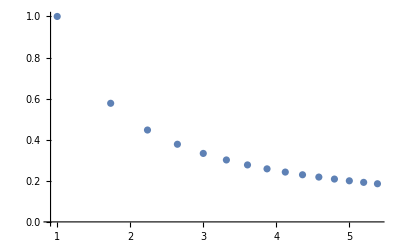

```mathematica
(*3. Предлагаю попробовать построить график из моих координат с помощью ListPoint.*)
ListPlot[{coords}]
```

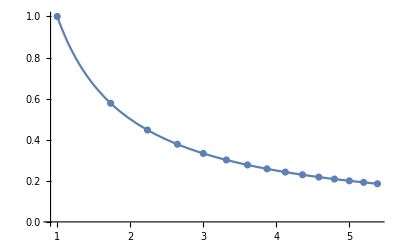

```mathematica
(*Отображу в одной графической области графики функции из первого пункта и из второго:*)
Show[ListPlot[{coords}],ParametricPlot[{x[t],y[t]},{t,a,b}]]
```

{{{2},{1,1}},{{4},{√3,1/(√3)}},{{6},{√5,1/(√5)}},{{8},{√7,1/(√7)}},{{10},{3,1/3}},{{12},{√11,1/(√11)}},{{14},{√13,1/(√13)}},{{16},{√15,1/(√15)}},{{18},{√17,1/(√17)}},{{20},{√19,1/(√19)}},{{22},{√21,1/(√21)}},{{24},{√23,1/(√23)}},{{26},{5,1/5}},{{28},{3 √3,1/(3 √3)}},{{30},{√29,1/(√29)}}}

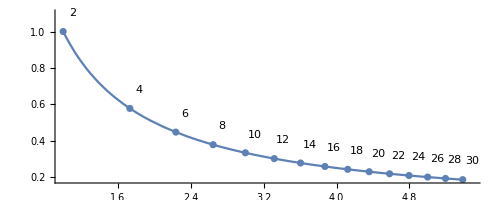

```mathematica
(*Подпишу каждую точку значением параметра, при котором вычислены её координаты. А так же сделаю красиво.*)
ClearAll[myCoordinatesAndValues]
myCoordinatesAndValues[x_,y_]:={{#},{x[#],y[#]}}&/@tValues
coordsValues=myCoordinatesAndValues[x,y]
{Text[#[[1]],#]&/@coordsValues};
Show[Graphics[{Text[First[#[[1]]],#[[2]]+0.1]&/@coordsValues,AspectRatio->Automatic,PlotRange->Automatic,Axes->True}],ListPlot[{coords}],ParametricPlot[{x[t],y[t]},{t,a,b},PlotRange->{{0,3},{0,4}}],Axes->True]
```